# Simple Scalar Code

This notebook provides simple, readable code for studying 2D ϕ^4 theory with Lightcone Conformal Truncation (LCT). Following section 4 of the paper, the emphasis here is on simplicity and conciseness, rather than efficiency. As a result, this code is useful only for low values of Δmax (<~10). However, this notebook performs all of the fundamental steps in LCT: constructing a truncated basis of primary operators, computing the Hamiltonian matrix elements in this basis, diagonalizing the truncated Hamiltonian, and computing observables in the deformed theory (e.g. spectral densities).

## Construct Basis

### Basis of Primary Operators

First we need to generate a complete basis of primary operators up to some maximum scaling dimension Δmax. To do so, we follow the procedure in section 4.1, gluing together multiple insertions of ∂ϕ with relative derivatives between them. These primaries are expressed as a sum of “monomials” ∂^k_1 ϕ...∂^k_n ϕ, which are each represented by the vector {k_(1,)...,k_n}. The “degree” of a monomial is defined as the total number of derivatives (k_1+...+k_n) minus the number of particles (n), since each particle must have at least one derivative acting on it (k_i≥ 1).

```mathematica
(*List the full set of monomials for a given particle number n_ and degree deg_. This function defines the canonical ordering of such monomials, which we will always use when expressing primary operators as vectors in the space of monomials*) 
monomialsBoson[n_,deg_]:=IntegerPartitions[deg+n,{n}];

(*The number of primary operators for a given particle number n_ and degree deg_*)
numStates[n_,deg_]:=Length[monomialsBoson[n,deg]]-Length[monomialsBoson[n,deg-1]];

(*Coefficients needed to glue together two "seed" primary operators A and B to construct a new primary operator with dimension Subscript[Δ, A]+Subscript[Δ, B]+ℓ*)
PrimCoeffs[DA_,DB_,l_,k_]:=(-1)^k Gamma[2DA+l]Gamma[2DB+l]/(k!(l-k)!Gamma[2DA+k]Gamma[2DB+l-k]);

(*Map that adds a additional ∂^k ϕ to the list of monomials with particle number n_ and degree deg_*)
appendOneScalarMapSimp[n_,deg_,dk_]:=Table[If[Reverse[Sort[Append[mon2,dk]]]==mon1,1,0],{mon2,monomialsBoson[n,deg]},{mon1,monomialsBoson[n+1,deg+dk-1]}];

(*Map that acts with a derivative on the list of monomials with particle number n_ and degree deg_*)
dBosonSimp[n_,deg_]:=Table[Length[Cases[Table[temp=mon2;temp[[i]]++;
Reverse[Sort[temp]],{i,n}],mon1]],{mon2,monomialsBoson[n,deg]},{mon1,monomialsBoson[n,deg+1]}];

(*Construct all primary operators at a fixed particle number n_ and degree deg_*)
PrimarySetSimp[n_,deg_]:=Block[{dl,vecs,vecsF,res={}},If[n==1,If[deg==0,res={{1}},res={}],Do[If[numStates[n-1,degP]≠0,dl=deg-degP;
vecs=PrimarySetSimp[n-1,degP];
vecsF=Table[0,{Length[vecs]},{Length[monomialsBoson[n,deg]]}];
Do[vecsF+=PrimCoeffs[degP+(n-1),1,dl,k]*Dot[vecs,appendOneScalarMapSimp[n-1,k+degP,dl-k+1]];
vecs=Dot[vecs,dBosonSimp[n-1,k+degP]],{k,0,dl}];
res=Join[res,vecsF]],{degP,deg,0,-n}]];
res];
```

EXAMPLES :

We can generate all monomials with n=2 and deg=2 (which correspond to ∂^3 ϕ∂ϕ and ∂^2 ϕ∂^2 ϕ) with monomialsBoson[]:

```mathematica
monomialsBoson[2,2]
```

{{3,1},{2,2}}

Starting with the one-particle state ∂ϕ, we can append a factor of ∂^3 ϕ with appendOneScalarMapSimp[] (the output is a vector in the space of n=2, deg=2 monomials):

```mathematica
appendOneScalarMapSimp[1,0,3]
```

{{1,0}}

We can act with a derivative on ∂^2 ϕ∂ϕ with dBosonSimp[] (the output is a vector in the space of n=2, deg=2 monomials):

```mathematica
dBosonSimp[2,1]
```

{{1,1}}

We can generate all primaries with n=2 and deg=2 with PrimarySetSimp[]:

```mathematica
PrimarySetSimp[2,2]
```

{{6,-9}}

Finally, we can use this code to generate the complete set of primary operators up to Δmax=5:

```mathematica
Δmax=5;
Table[Table[prim.(Dot@@Table[d^k ϕ,{k,#}]&)/@monomialsBoson[n,Δ-n],{prim,PrimarySetSimp[n,Δ-n]}],{n,Δmax},{Δ,Δmax}]//MatrixForm
```

({d ϕ} | {} | {} | {} | {}
{} | {(d ϕ).(d ϕ)} | {} | {-9 (d^2 ϕ).(d^2 ϕ)+6 (d^3 ϕ).(d ϕ)} | {}
{} | {} | {(d ϕ).(d ϕ).(d ϕ)} | {} | {-9 (d^2 ϕ).(d^2 ϕ).(d ϕ)+6 (d^3 ϕ).(d ϕ).(d ϕ)}
{} | {} | {} | {(d ϕ).(d ϕ).(d ϕ).(d ϕ)} | {}
{} | {} | {} | {} | {(d ϕ).(d ϕ).(d ϕ).(d ϕ).(d ϕ)})

### Orthonormalize Basis

Next we need to orthonormalize our list of primary operators. To do so, we follow the procedure in section 4.2, first computing the Gram matrix for all monomials, then orthonormalizing the primaries generated by PrimarySetSimp[] with respect to this Gram matrix.

```mathematica
(*Wick contraction coefficients between two monomials*)
A[k_,kp_]:=If[Length[kp]≤1,Product[Gamma[k[[i]]+kp[[i]]],{i,Length[kp]}],Sum[Gamma[k[[-1]]+kp[[i]]]A[Delete[k,-1],Delete[kp,i]],{i,Length[kp]}]];

(*Construct the Gram matrix for all monomials of fixed particle number n_ and degree deg_*)
monoGram[n_,deg_]:=Table[Sqrt[Gamma[2Total[k]]Gamma[2Total[kp]]]/Gamma[Total[k+kp]]*A[k,kp]/Sqrt[A[k,k]A[kp,kp]],{k,monomialsBoson[n,deg]},{kp,monomialsBoson[n,deg]}];

(*Rescale the coefficients generated by PrimarySetSimp[] to include the monomial normalization*)
rescalePrimarySet[n_,deg_]:=Table[Sqrt[A[mono,mono]],{i,numStates[n,deg]},{mono,monomialsBoson[n,deg]}]*PrimarySetSimp[n,deg];

(*Orthonormalize all basis states of fixed particle number n_ and degree deg_*)
orthoPrimaries[n_,deg_]:=FullSimplify[Orthogonalize[rescalePrimarySet[n,deg],#1.monoGram[n,deg].#2&]];
```

EXAMPLES :

We can compute the Gram matrix for all n=2, deg=2 monomials with monoGram[]:

```mathematica
monoGram[2,2]
```

{{1,4 √(2/39)},{4 √(2/39),1}}

We can rescale the coefficients for the primary operator  6∂^3 ϕ∂ϕ-9∂^2 ϕ∂^2 ϕ to account for the monomial normalizations with rescalePrimarySet[]:

```mathematica
rescalePrimarySet[2,2]
```

{{12 √39,-54 √2}}

We can generate the orthonormal set of basis states with n=2, deg=2 with orthoPrimaries[]:

```mathematica
orthoPrimaries[2,2]//FullSimplify
```

{{√(26/5),-3 √(3/5)}}

Finally, we can generate the orthonormal primary basis up to Δmax=5:

```mathematica
Δmax=5;
Table[orthoPrimaries[n,Δ-n]//FullSimplify,{n,Δmax},{Δ,Δmax}]//MatrixForm
```

({{1}} | {} | {} | {} | {}
{} | {{1}} | {} | {{√(26/5),-3 √(3/5)}} | {}
{} | {} | {{1}} | {} | {{8/(√7),-3}}
{} | {} | {} | {{1}} | {}
{} | {} | {} | {} | {{1}})

## Matrix Elements

Once we’ve computed the primary basis up to some Δmax, we can then compute the Hamiltonian matrix elements in this basis. Here we compute the matrix elements for the ϕ^2 (mass term) and ϕ^4 (quartic interaction) deformations. The mass term is diagonal with respect to particle number, while the quartic interaction has two contributions: one which preserves particle number (n-to-n) and one which changes particle number by 2 (n-to-n+2).

### Mass Term

```mathematica
(*Mass term matrix element for one incoming monomial (k_) and one outgoing monomial (kp_)*)
monoMass[k_,kp_]:=Sqrt[Gamma[2Total[k]]Gamma[2Total[kp]]/(A[k,k]A[kp,kp])]/Gamma[Total[k+kp]-1]Sum[Gamma[k[[i]]+kp[[j]]-1]A[Delete[k,i],Delete[kp,j]],{i,Length[k]},{j,Length[kp]}];

(*Generate the mass term matrix elements between all n-particle basis states with incoming degree deg1_ and outgoing degree deg2_*)
primaryMassMatrix[n_,deg1_,deg2_]:=If[numStates[n,deg1]==0||numStates[n,deg2]==0,{},
orthoPrimaries[n,deg1].Table[monoMass[k,kp],{k,monomialsBoson[n,deg1]},{kp,monomialsBoson[n,deg2]}].Transpose[orthoPrimaries[n,deg2]]];
```

EXAMPLES :

We can compute the mass term matrix element between ∂ϕ∂ϕ and ∂ϕ∂ϕ with primaryMassMatrix[]:

```mathematica
primaryMassMatrix[2,0,0]
```

{{6}}

We can then generate all mass term matrix elements up to Δmax=5:

```mathematica
Δmax=5;
mass=ConstantArray[{},{Δmax,Δmax}];
For[n=1,n≤Δmax,n++,
mass[[n,n]]=Table[primaryMassMatrix[n,Δ1-n,Δ2-n]//FullSimplify,{Δ1,Δmax},{Δ2,Δmax}]//Replace[#,x_List:>DeleteCases[x,{}],{0,Infinity}]&;
];
(mass//ArrayFlatten)/.{{}->0}//ArrayFlatten//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | √14 | 0 | 0 | 0 | 0
0 | √14 | 14 | 0 | 0 | 0 | 0
0 | 0 | 0 | 15 | 4 √3 | 0 | 0
0 | 0 | 0 | 4 √3 | 27 | 0 | 0
0 | 0 | 0 | 0 | 0 | 28 | 0
0 | 0 | 0 | 0 | 0 | 0 | 45)

### ϕ^4 Interaction

```mathematica
(*ϕ^4 n-to-n matrix element for one incoming monomial (k_) and one outgoing monomial (kp_)*)
monoNtoN[k_,kp_]:=Sqrt[Gamma[2Total[k]]Gamma[2Total[kp]]/(A[k,k]A[kp,kp])]/Gamma[Total[k+kp]-1]Sum[Gamma[k[[i]]]Gamma[k[[j]]]Gamma[kp[[r]]]Gamma[kp[[s]]]Gamma[k[[i]]+k[[j]]+kp[[r]]+kp[[s]]-1]/(Gamma[k[[i]]+k[[j]]]Gamma[kp[[r]]+kp[[s]]])A[Delete[k,{{i},{j}}],Delete[kp,{{r},{s}}]],{i,Length[k]},{j,i-1},{r,Length[kp]},{s,r-1}];

(*ϕ^4 n-to-n+2 matrix element for one incoming monomial (k_) and one outgoing monomial (kp_)*)
monoNtoNplus2[k_,kp_]:=Sqrt[Gamma[2Total[k]]Gamma[2Total[kp]]/(A[k,k]A[kp,kp])]/Gamma[Total[k]+Total[kp]-1]Sum[Gamma[kp[[r]]]Gamma[kp[[s]]]Gamma[kp[[t]]]Gamma[k[[i]]+kp[[r]]+kp[[s]]+kp[[t]]-1]/Gamma[kp[[r]]+kp[[s]]+kp[[t]]]A[Delete[k,i],Delete[kp,{{r},{s},{t}}]],{i,Length[k]},{r,Length[kp]},{s,r-1},{t,s-1}];

(*Generate the ϕ^4 n-to-n matrix elements between all n-particle basis states with incoming degree deg1_ and outgoing degree deg2_*)
primaryNtoNMatrix[n_,deg1_,deg2_]:=If[numStates[n,deg1]==0||numStates[n,deg2]==0,{},
orthoPrimaries[n,deg1].Table[monoNtoN[k,kp],{k,monomialsBoson[n,deg1]},{kp,monomialsBoson[n,deg2]}].Transpose[orthoPrimaries[n,deg2]]];

(*Generate the ϕ^4 n-to-n+2 matrix elements between all n-particle basis states with incoming degree deg1_ and n+2-particle states with outgoing degree deg2_*)
primaryNtoNplus2Matrix[n_,deg1_,deg2_]:=If[numStates[n,deg1]==0||numStates[n+2,deg2]==0,{},
orthoPrimaries[n,deg1].Table[monoNtoNplus2[k,kp],{k,monomialsBoson[n,deg1]},{kp,monomialsBoson[n+2,deg2]}].Transpose[orthoPrimaries[n+2,deg2]]];
```

EXAMPLES :

We can compute the ϕ^4 matrix element between ∂ϕ∂ϕ and ∂ϕ∂ϕ with primaryNtoNMatrix[]:

```mathematica
primaryNtoNMatrix[2,0,0]
```

{{3}}

```mathematica
primaryNtoNMatrix[2,0,0]
```

{{3}}

We can compute the ϕ^4 matrix element between ∂ϕ and ∂ϕ∂ϕ∂ϕ with primaryNtoNplus2Matrix[]:

```mathematica
primaryNtoNplus2Matrix[1,0,0]
```

{{√5}}

We can then generate all ϕ^4 n-to-n matrix elements up to Δmax=5:

```mathematica
Δmax=5;
int=ConstantArray[{},{Δmax,Δmax}];
For[n=1,n≤Δmax,n++,
int[[n,n]]=Table[primaryNtoNMatrix[n,Δ1-n,Δ2-n]//FullSimplify,{Δ1,Δmax},{Δ2,Δmax}]//Replace[#,x_List:>DeleteCases[x,{}],{0,Infinity}]&;
];
For[n=1,n≤Δmax-2,n++,
int[[n,n+2]]=Table[primaryNtoNplus2Matrix[n,Δ1-n,Δ2-n-2]//FullSimplify,{Δ1,Δmax},{Δ2,Δmax}]//Replace[#,x_List:>DeleteCases[x,{}],{0,Infinity}]&;
int[[n+2,n]]=int[[n,n+2]]//Transpose;
];
(int//ArrayFlatten)/.{{}->0}//ArrayFlatten//MatrixForm
```

(0 | 0 | 0 | √5 | (√15)/2 | 0 | 0
0 | 3 | √(7/2) | 0 | 0 | √70 | 0
0 | √(7/2) | 7/6 | 0 | 0 | 0 | 0
√5 | 0 | 0 | 15 | 4 √3 | 0 | 2 √105
(√15)/2 | 0 | 0 | 4 √3 | 33/2 | 0 | 0
0 | √70 | 0 | 0 | 0 | 42 | 0
0 | 0 | 0 | 2 √105 | 0 | 0 | 90)

### Diagonalize Full Hamiltonian

We now have all of the ingredients we need to construct and diagonalize the Hamiltonian! For example, we can plot the lowest eigenvalue (i.e. the mass gap) as a function of the coupling λ/(4π) (in units where the bare mass m^2=1):

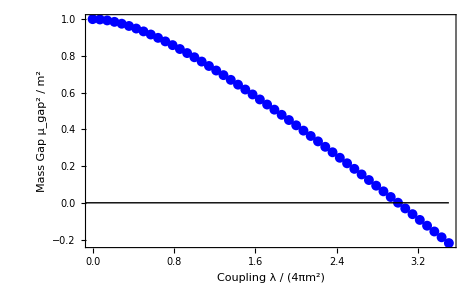

```mathematica
Δmax=5;

(*Construct mass term*)
mass=ConstantArray[{},{Δmax,Δmax}];
For[n=1,n≤Δmax,n++,
mass[[n,n]]=Table[primaryMassMatrix[n,Δ1-n,Δ2-n]//FullSimplify,{Δ1,Δmax},{Δ2,Δmax}]//Replace[#,x_List:>DeleteCases[x,{}],{0,Infinity}]&;
];
mass=(mass//ArrayFlatten)/.{{}->0}//ArrayFlatten;

(*Construct ϕ^4 interaction term*)
int=ConstantArray[{},{Δmax,Δmax}];
For[n=1,n≤Δmax,n++,
int[[n,n]]=Table[primaryNtoNMatrix[n,Δ1-n,Δ2-n]//FullSimplify,{Δ1,Δmax},{Δ2,Δmax}]//Replace[#,x_List:>DeleteCases[x,{}],{0,Infinity}]&;
];
For[n=1,n≤Δmax-2,n++,
int[[n,n+2]]=Table[primaryNtoNplus2Matrix[n,Δ1-n,Δ2-n-2]//FullSimplify,{Δ1,Δmax},{Δ2,Δmax}]//Replace[#,x_List:>DeleteCases[x,{}],{0,Infinity}]&;
int[[n+2,n]]=int[[n,n+2]]//Transpose;
];
int=(int//ArrayFlatten)/.{{}->0}//ArrayFlatten;

(*Scan over λ/(4π) with m^2=1, diagonalize the Hamiltonian, and store the lowest eigenvalue*)
λmax=3.5;
numPts=50;
dλ=λmax/(numPts-1);
λlist=Table[(i-1)*dλ,{i,numPts}];
gap=ConstantArray[0,numPts];
For[iL=1,iL≤numPts,iL++,
hamiltonian=mass+λlist[[iL]]*int;
gap[[iL]]=Eigenvalues[hamiltonian]//Min;
];

(*Plot the mass gap (lowest eigenvalue) as a function of the coupling*)
plot=ListPlot[Thread[{λlist,gap}],PlotRange->{{0,λmax},Automatic},PlotStyle->{Blue,PointSize[0.015]},Frame->True,FrameStyle->Thickness[0.002],FrameLabel->{Style["Coupling  λ / (4πm^2)",FontFamily->"Times",FontSize->18,FontColor->Black],Style["Mass Gap  μ_gap^2 / m^2",FontFamily->"Times",FontSize->18,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->475];
line=Plot[0,{x,-λmax,λmax},PlotStyle->{Black,Thick}];
Show[plot,line]
```

## Spectral Densities

Once we’ve diagonalized the full Hamiltonian for some value of Δmax, we can use the eigenvectors to compute observables in the deformed theory. One simple observable is the spectral density of a local operator 𝒪, which measures the overlap of 𝒪 with the mass eigenstates. To compute this, we need to first compute the overlap of our basis states with the operator 𝒪. In scalar field theory, one obvious set of operators to study is ϕ^n. Here we compute the overlaps of our basis states with ϕ^n, which can then be used to study spectral densities.

### Overlap with ϕ^n

```mathematica
(*Overlap of one monomial (k_) with ϕ^n*)
monoPhiN[k_]:=Length[k]!Product[Gamma[k[[i]]],{i,Length[k]}]/Gamma[Total[k]]Sqrt[Gamma[2Total[k]]/((4Pi)^(Length[k]-1)A[k,k])];

(*Overlap of all primary operators with number of particles n_ and degree deg_ with ϕ^n*)
primaryPhiN[n_,deg_]:=If[numStates[n,deg]==0,{},
orthoPrimaries[n,deg].Table[monoPhiN[k],{k,monomialsBoson[n,deg]}]];
```

EXAMPLES :

We can compute the overlap of the basis state ∂ϕ∂ϕ with ϕ^2 with primaryPhiN[]:

```mathematica
primaryPhiN[2,0]
```

{√(3/π)}

In general, we need larger values of Δmax to reproduce spectral densities. Fortunately, if we study free massive theory (λ=0) we can focus solely on the two-particle sector, where we can push to Δmax=20 and reproduce the integrate spectral density of ϕ^2:

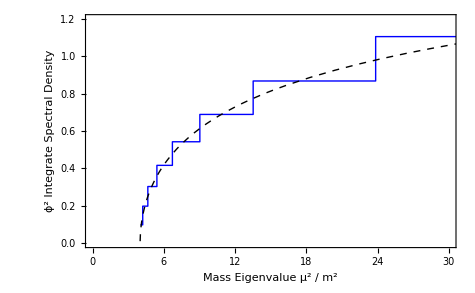

```mathematica
Δmax=20;

(*Compute the overlap of ϕ^2 with all two-particle primaries*)
overlaps=Table[primaryPhiN[2,Δ-2]//FullSimplify,{Δ,2,Δmax,2}]//Flatten;

(*Construct two-particle mass term*)
mass=(Table[primaryMassMatrix[2,Δ1-2,Δ2-2]//FullSimplify,{Δ1,2,Δmax,2},{Δ2,2,Δmax,2}]//Replace[#,x_List:>DeleteCases[x,{}],{0,Infinity}]&)//ArrayFlatten;

(*Diagonalize mass term (sorting eigenvalues from smallest to largest), compute overlap of eigenvectors with ϕ^2, and sum to obtain integrated spectral density*)
{vals,vecs}=mass//N//Eigensystem//Transpose//Sort//Transpose;
specs=vecs.overlaps;
specSum=Accumulate[Abs[specs]^2];

(*Plot the integrated spectral density of ϕ^2, compared to the theoretical prediction*)
theory=Plot[(2 Log[√x+√(x-4)]-Log[4])/π,{x,0,100},PlotStyle->{Black,Dashed,Thick}];
data=ListStepPlot[Thread[{vals,specSum}],PlotRange->{{0,30},{0,1.2}},PlotStyle->{Blue,Thick},Frame->True,FrameStyle->Thickness[0.002],FrameLabel->{Style["Mass Eigenvalue  μ^2 / m^2",FontFamily->"Times",FontSize->18,FontColor->Black],Style["ϕ^2 Integrate Spectral Density",FontFamily->"Times",FontSize->18,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->475];
Show[data,theory]
```